```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Thread Counting using Morphological Operations

People have highly developed visual abilities; it is easy to look at a complicated image and to make decisions about what objects are represented in the image and how many of these objects are present. This notebook represents a first pass at counting the number of threads per centimeter in an x-ray canvas using morphological operations. The methods adopted are somewhat primitive, but are motivated by an attempt to mimic the way that people would imagine that the canvas is a grid, and then count the number of rows and columns in the grid.

```mathematica
TableForm[{{Hyperlink["GridPoints",{"threadsMethodD.nb","labelGridPoints"},BaseStyle->appColor],labelGridPoints},{Hyperlink["ToGrid",{"threadsMethodD.nb","labelToGrid"},BaseStyle->appColor],labelToGrid},{Hyperlink["MorphAdapt",{"threadsMethodD.nb","labelMorphAdapt"},BaseStyle->appColor],labelMorphAdapt},{Hyperlink["MorphWavelet",{"threadsMethodD.nb","labelMorphWavelet"},BaseStyle->appColor],labelMorphWavelet},{Hyperlink["MorphSkel",{"threadsMethodD.nb","labelMorphSkel"},BaseStyle->appColor],labelMorphSkel}}]
```

GridPointsthreadsMethodD.nblabelGridPointsthreadsMethodD.nbHyperlinkHyperlinkActive | By proper choice of parameters, it may be possible to transform the raw image into a simple grid of points
ToGridthreadsMethodD.nblabelToGridthreadsMethodD.nbHyperlinkHyperlinkActive | By proper choice of neighborhood, it may be possible to transform the raw image into a regular grid of lines
MorphAdaptthreadsMethodD.nblabelMorphAdaptthreadsMethodD.nbHyperlinkHyperlinkActive | Adaptive thresholding cleans up the images so that an ultimate erosion can pinpoint the majority of the thread intersections
MorphWaveletthreadsMethodD.nblabelMorphWaveletthreadsMethodD.nbHyperlinkHyperlinkActive | Wavelets are used to emphasize the vertical and horizontal directions, and the result is processed using ultimate erosion as above
MorphSkelthreadsMethodD.nblabelMorphSkelthreadsMethodD.nbHyperlinkHyperlinkActive | The morphological skeleton applied to canvas x-rays

Important commands in the notebook are the morphological functions.

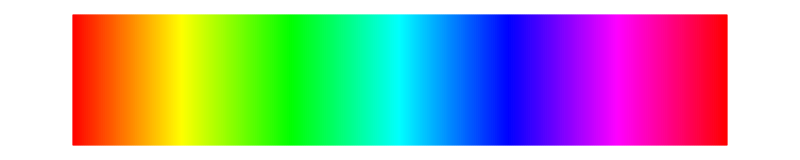

```mathematica
specLine
```

To motivate the approach, consider applying dilation and erosion to the rectangle model, to the functional model, and to an x-ray tile.

```mathematica
labelGridPoints="By proper choice of parameters, it may be possible to transform the raw image into a simple grid of points";
infoGridPoints="Using basic morphological operators such as erosion and dilation, small connected areas can sometimes be reduced to points. \n\nThe two operations are applied to both the positive and negative of the image, and the results may depend on the threshold for binarization.";
Manipulate[Module[{img},
If[invert=="negative",img=allIm[[i]],img=ColorNegate[allIm[[i]]]];
Grid[{{
Labeled[img,Text@"raw image"],
Labeled[Dilation[Binarize[img, s], r],Text@"dilation"], Labeled[Dilation[Binarize[ColorNegate[img],s],r],Text@"dilation of negative"]},{Labeled[Binarize[img, s],Text@"binary version"],
 Labeled[Erosion[Binarize[img, s], r],Text@"erosion"],Labeled[Erosion[Binarize[ColorNegate[img],s],r],Text@"erosion of negative"]}}]], Row[{Control[{{i,2,"image"},Thread[Range[Length[allIm]]->allImNames],ControlType->PopupMenu}],Spacer[20],Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[20],info[infoGridPoints]}],
{{s,0.5,"threshold for binarization"},0,1},
{{r, 3,"morphological neighborhood"}, 1, 30,1},FrameLabel->Style[labelGridPoints,Medium],TrackedSymbols->{i,s,r,invert},SaveDefinitions->True]
```

Both erosion and dilation can be made to work quite effectively on the models, but the real image needs more care. The bulk of this notebook will explore a variety of preprocessing methods (some morphological, some linear filters, some nonlinear filters, some transforms) that may help to improve the ability of the operations to extract the desired grid of points from the image.

```mathematica
specLine
```

-Graphics-

Perhaps the first thing to try is to change the shape of the structuring element. Instead of a r by r neighborhood as above, consider using a short-fat structuring element to try and bring out the horizontal parts (presumably followed by a tall-skinny structuring element to bring out the vertical parts). As the following interactive example shows, it is again easy to make this work for the (simplified) models, but more tricky to make it work for real data.

```mathematica
labelToGrid="By proper choice of neighborhood, it may be possible to transform the raw image into a regular grid of lines";
infoToGrid="Using a long-thin horizontal neighborhood tends to bring out horizontal features. \n\nWith the default values, the erosion of the negative shows a horizontal line across each horizontal thread (at least for the rectangle model). \n\nHow well can you make it work for the top-view model and the x-ray tile? \n\nBy proper choice of threshold, can you make the dilation perform a similar task?";
kern[size_]:=ConstantArray[1,{3,size}];
Manipulate[
Module[{img},
If[invert=="negative",img=allIm[[i]],img=ColorNegate[allIm[[i]]]];Grid[{{Labeled[img,Text@"raw image"],Labeled[Dilation[Binarize[img,s],kern[r]],Text@"dilation"],Labeled[Dilation[Binarize[ColorNegate[img],s],kern[r]],Text@"dilation of negative"]},{Labeled[Binarize[img,s],Text@"binary version"],Labeled[Erosion[Binarize[img,s],kern[r]],Text@"erosion"],Labeled[Erosion[Binarize[ColorNegate[img],s],kern[r]],Text@"erosion of negative"]}}]],Row[{Control[{{i,2,"image"},Thread[Range[Length[allIm]]->allImNames],ControlType->PopupMenu}],Spacer[20],
Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[20],info[infoToGrid]}],
{{s,0.044,"threshold for binarization"},0,1},{{r,100,"morphological neighborhood"},1,100,1},FrameLabel->Style[labelToGrid,Medium],TrackedSymbols->{i,s,r,invert},SaveDefinitions->True]
```

HW: Change the structuring element (the kernel) to be a CrossMatrix[ ] and try dilating and eroding using this shape.

```mathematica
(* ker2[size_]:=CrossMatrix[size];
allIm={ColorNegate[allImagesXray[[f634Tile]]],imgBoxes,imgSinSquare};
allImNames={"x-ray tile","rectangle model","functional model"};
Manipulate[Grid[{{Labeled[allIm[[i]],Text@"raw image"],Labeled[Dilation[Binarize[allIm[[i]],s],ker2[r]],Text@"dilation"],Labeled[Dilation[Binarize[ColorNegate[allIm[[i]]],s],ker2[r]],Text@"dilation of negative"]},{Labeled[Binarize[allIm[[i]],s],Text@"binary version"],Labeled[Erosion[Binarize[allIm[[i]],s],ker2[r]],Text@"erosion"],Labeled[Erosion[Binarize[ColorNegate[allIm[[i]]],s],ker2[r]],Text@"erosion of negative"]}}],{{i,2,"image"},Thread[Range[Length[allIm]]->allImNames],ControlType->PopupMenu},{{s,0.5,"threshold for binarization"},0,1},{{r,3,"morphological neighborhood"},1,100,1},FrameLabel->Style["By proper choice of parameters, it may be possible to transform the raw image into a simple grid of points",Medium],TrackedSymbols->{i,s,r},SaveDefinitions->True] *)
```

```mathematica
specLine
```

-Graphics-

One possible problem with the real data is that there may be areas that are generally dark and other areas that are generally light. Trying to binarize both of these with a single threshold value means that either one is overly black, the other is overly white, or both are somewhat compromised. A similar problem was solved in the nonlinear filters notebook using an adaptive thresholding function, which is adopted here. After the more sophisticated thesholding, there are many small blobs that can be shrunk using “ultimate erosion” which can be implemented using the DistanceTransform[ ] followed by MaxDetect[].

```mathematica
labelMorphAdapt="Adaptive thresholding cleans up the images so that an ultimate erosion can pinpoint the majority of the thread intersections";
infoMorphAdapt="Using an adaptive threshold as a preprocessor for the the grid detection can help to make the results more uniform (and hence more useful). \n\nThe x-ray tile (left) is binarized with an adaptive threshold (middle). Ultimate erosion (implemented using the Distance transform and MaxDetect[]) then locates the center of each element. \n\nTry the default values on various images, observe that the output is fairly robust to these parameter choices.";
Manipulate[Module[{img,adaptImg},
If[invert=="negative",img=allImagesXray[[i]],img=ColorNegate[allImagesXray[[i]]]];
threshRat=tau;
GraphicsRow[{img,
adaptImg=ImageFilter[adaptThresh,img,n],
Dilation[MaxDetect[DistanceTransform[ColorNegate[adaptImg]]],1]},ImageSize->900]],
Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],Control[{{invert,"positive",""},{"negative","positive"}}],Spacer[20],info[infoMorphAdapt]}],
{{n,9,"adaptive neighborhood"},1,30,1},
{{tau,1,"threshold ratio"},0.95,1.1},
FrameLabel->Style[labelMorphAdapt,Medium],SynchronousUpdating->False,TrackedSymbols->{i,n,r,tau,invert},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

An alternative method of cleaning up the thread images before applying the morphological processing is to use the wavelet transform. In this example, the wavelet coefficients in the horizontal direction are amplified, the coefficients in the vertical direction are amplified, and then the two are multiplied together. This results in a cleaner grid, which is then processed using an adaptive threshold (including a closing operation to remove some possible small white imperfections). The final step is an ultimate erosion to reduce the small blocks to points. More information about this kind of wavelet enhancement is here.

```mathematica
labelMorphWavelet="Wavelets are used to emphasize the vertical and horizontal directions, and the result is processed using ultimate erosion as above";
infoMorphWavelet="Instead of using a long-thin neighborhood, a similar effect can be obtained by augmenting the appropriate horizontal and vertical scale elements in the wavelet decomposition (the middle and right images in the top row). \n\nThe product of these two wavelet filterings is then a cleaned up version (bottom left) which is adaptively thresholded and morphologically opened to reomve small uninteresting white spots (middle bottom). \n\nThe final step is an ultimate erosion to leave only a single point in each region of interest.";
Manipulate[Module[{imgX,swt,mapWaveH,mapWaveV,invH,invV,adaptImg,prodHV},
If[invert=="negative",imgX=allImagesXray[[i]],imgX=ColorNegate[allImagesXray[[i]]]];swt=StationaryWaveletTransform[imgX,ShannonWavelet[]];
mapWaveH=WaveletMapIndexed[ImageMultiply[#,20]&,swt,{0,0,2}];
mapWaveV=WaveletMapIndexed[ImageMultiply[#,20]&,swt,{0,0,1}];
GraphicsGrid[{{imgX,invH=InverseWaveletTransform[mapWaveH,ShannonWavelet[]],invV=InverseWaveletTransform[mapWaveV,ShannonWavelet[]]},{prodHV=ImageMultiply[invH,invV],adaptImg=Opening[ImageFilter[adaptThresh,prodHV,9],2],Dilation[MaxDetect[DistanceTransform[ColorNegate[adaptImg]]],1]}},ImageSize->900]],Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[20],info[infoMorphWavelet]}],FrameLabel->Style[labelMorphWavelet,Medium],SynchronousUpdating->False,TrackedSymbols->{i,n,invert},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

Yet another possible source of preprocessing is morphological skeletonization.

```mathematica
labelMorphSkel="The morphological skeleton applied to canvas x-rays";
infoMorphSkel="The skeleton reduces each white segment of an image to a thin framework. This can also be a powerful preprocessing tool for the location of the underlying grid points of the x-ray tiles. \n\nConsider skeletonizing the positive x-ray; what is the source of all the small boxes? Can this be useful as well in determining the thread count? \n\nThe skeletonization is done two ways: by iterating the Erosion-Opening[Erosion] and by using the Thinning[] command.";
Manipulate[Module[{img},
If[invert=="negative",img=allImagesXray[[i]],img=ColorNegate[allImagesXray[[i]]]];
GraphicsRow[{img,ImageAdjust[Image[Total[Table[ImageData[ImageSubtract[Erosion[img,r],Opening[Erosion[img,r],1]]],{r,1,20}]]]],ImageAdjust[Thinning[img,10,t]]},ImageSize->900]],Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[30],Control[{{invert,"positive",""},{"negative","positive"}}],Spacer[30],Control[{{t,0.5,"threshold"},0,1}],Spacer[20],info[infoMorphSkel]}],FrameLabel->Style[labelMorphSkel,Medium],SynchronousUpdating->False,TrackedSymbols->{i,invert,t},SaveDefinitions->saveDef]
```

HW: Can the skeletonization be made more effective if the image is preprocessed using the adaptive thresholding method?

HW: Choose one of the methods above and carry it through to completion, that is, make an algorithm to count the rows/columns of the processed image so as to return an estimate of the thread count.